```mathematica
Minimize[Sin[x]-Cos[y]+Sin[x]-x^2+2x,{x,y}]
```

Minimize[2 x-x^2-Cos[y]+2 Sin[x],{x,y}]

```mathematica
eqs={
{Sin[x/2]^2-Sin[y]^7,{x,y},{-2,1}},
{Sin[x]-Sin[y],{x,y},{-3,1}},
{Sin[x^2]-Sin[y],{x,y},{-4,4}},
{Sin[x-y]-Cos[y],{x,y},{-4,4}},
{(x y-3)^2+1,{x,y},{-10,1}},
{100-Sin[x+Sin[y]]+Sin[y+Sin[x]],{x,y},{-10,1}},
{Sin[x]-Sin[y]+x^2+2x,{x,y},{-10,1}}
};
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

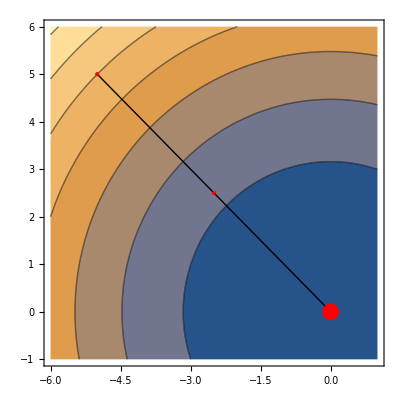
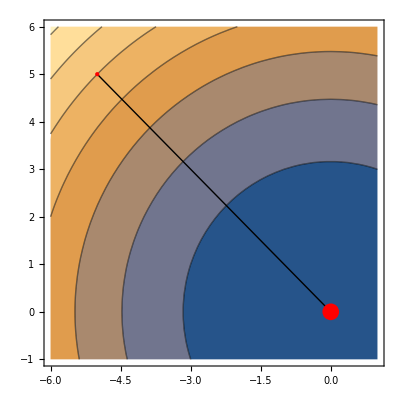
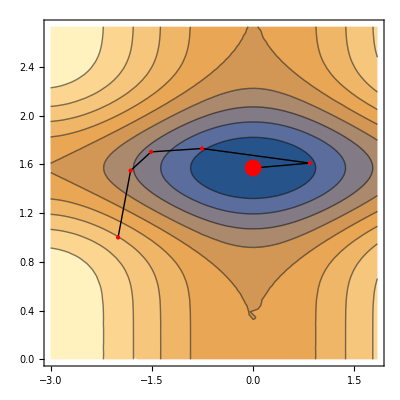
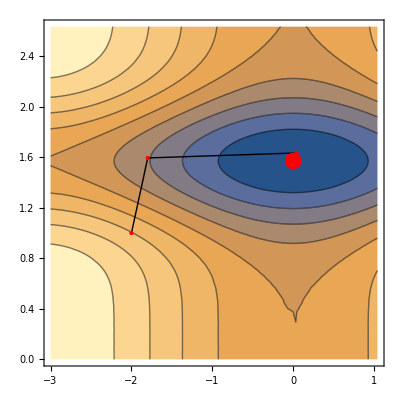
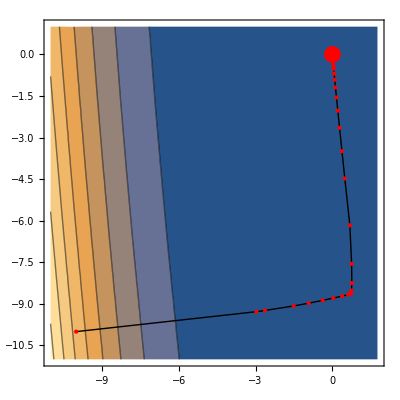
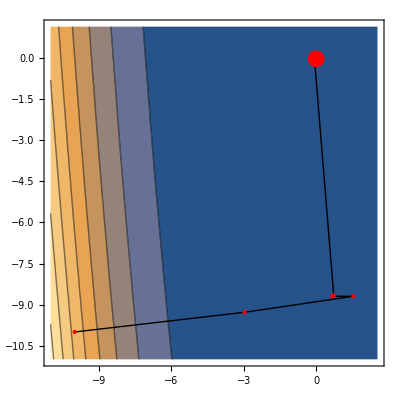
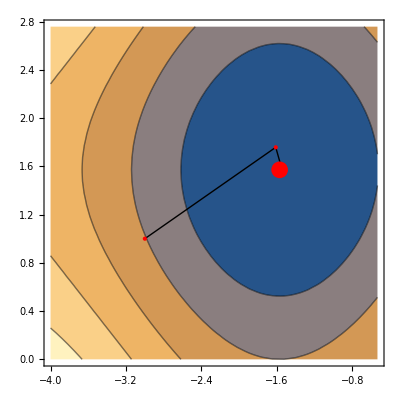
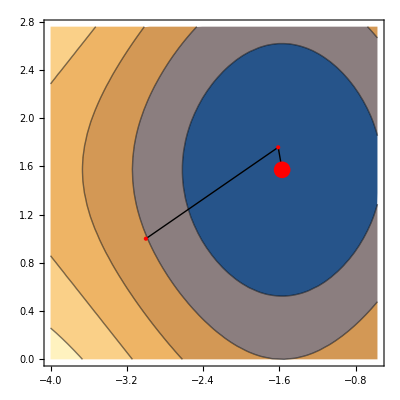
x^2+y^2 | -Graphics-Function Evaluation Count = 3, Iteration Count = 2 | -Graphics-Function Evaluation Count = 7, Iteration Count = 3
sin^2(x/2) | -Graphics-Function Evaluation Count = 11, Iteration Count = 9 | -Graphics-Function Evaluation Count = 19, Iteration Count = 7
x^4+(x+y/6)^4 | -Graphics-Function Evaluation Count = 87, Iteration Count = 82 | -Graphics-Function Evaluation Count = 36, Iteration Count = 10
sin(x) | -Graphics-Function Evaluation Count = 9, Iteration Count = 8 | -Graphics-Function Evaluation Count = 12, Iteration Count = 4
sin(x^2) | -Graphics-Function Evaluation Count = 20, Iteration Count = 13 | -Graphics-Function Evaluation Count = 35, Iteration Count = 11
-cos(y) | -Graphics-Function Evaluation Count = 11, Iteration Count = 8 | -Graphics-Function Evaluation Count = 25, Iteration Count = 10
100 | -Graphics-Function Evaluation Count = 14, Iteration Count = 12 | -Graphics-Function Evaluation Count = 35, Iteration Count = 11
2 x | -Graphics-Function Evaluation Count = 10, Iteration Count = 9 | -Graphics-Function Evaluation Count = 16, Iteration Count = 6
x y | -Graphics-Function Evaluation Count = 12, Iteration Count = 2 | -Graphics-Function Evaluation Count = 28, Iteration Count = 3
sin(Abs[x y]) | -Graphics-Function Evaluation Count = 80, Iteration Count = 10 | -Graphics-Function Evaluation Count = 144, Iteration Count = 13
cos^2(y) | -Graphics-Function Evaluation Count = 25, Iteration Count = 10 | -Graphics-Function Evaluation Count = 41, Iteration Count = 10
ⅇ | -Graphics-Function Evaluation Count = 101, Iteration Count = 100 | -Graphics-Function Evaluation Count = 3, Iteration Count = 2

```mathematica
PrependTo[$Path,NotebookDirectory[]];
<<implementation.m;
Grid[
Table[
CompareMethods[Evaluate[Sequence@@eq]],
{eq,{
{{x^2+y^2},{x,y},{-5,5}},
{Sin[x/2]^2-Sin[y]^7,{x,y},{-2,1}},
{{x^4+(y/6+x)^4},{x,y},{-10,-10}},
{Sin[x]-Sin[y],{x,y},{-3,1}},
{Sin[x^2]-Sin[y],{x,y},{-4,4}},
{Sin[x-y]-Cos[y],{x,y},{-4,4}},
{100-Sin[x+Sin[y]]+Sin[y+Sin[x]],{x,y},{-10,1}},
{Sin[x]-Sin[y]+x^2+2x,{x,y},{-10,1}},
{Abs[x y],{x,y},{1,1}},
{Sin@Abs[x y]+Sin@Cos[y],{x,y},{1,1}},
{Cos[y]^2+Sin[x y],{x,y},{-3,-3}},
{Exp[x - y],{x,y},{-3,-3}}
}
}
]
]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"exp.png"}],%,ImageSize->Scaled[2]]
```

C:\Users\adakk_000\Documents\GitHub\CS544\hw1\exp.png

```mathematica
Labeled
```

```mathematica
m["StepCount"]
```

37

```mathematica
m
```

MinimumInformation[<|Function→Sin[x] Sin[2 y],Variables→{x,y},Start→{-1.2,1},Points→{{-1.2,1.},{-1.45734,0.394135},{-1.30156,0.760885},{-1.39884,0.762973},{-1.57471,0.787762},{-1.57084,0.785255},{-1.57079,0.785401},{-1.5708,0.785398},{-1.5708,0.785398}},Solution→{-1.,{x→-1.5708,y→0.785398}}|>]

```mathematica
Min[m["Points"][[All,{1}]]]
```

-1.57471

```mathematica
m["Points"][[All,{2}]]
```

{{1.},{0.394135},{0.760885},{0.762973},{0.787762},{0.785255},{0.785401},{0.785398},{0.785398}}

```mathematica
m["Points"]
```

{{-1.2,1.},{-1.45734,0.394135},{-1.30156,0.760885},{-1.39884,0.762973},{-1.57471,0.787762},{-1.57084,0.785255},{-1.57079,0.785401},{-1.5708,0.785398},{-1.5708,0.785398}}

```mathematica
Attributes[FindMinimum]
```

{HoldAll,Protected}

```mathematica
pts = Reap[FindMinimum[1+(1-x)^2+100(-x^2-y)^2,{{x,-1.2},{y,1}},StepMonitor:>Sow[{x,y}]]][[2,1]];
pts =Join[{{-1.2,1}},pts];
pts = With[{f=Hold[1+(1-x)^2+100 (-x^2-y)^2]},
Print[f];
Reap[FindMinimum[(1-x)^2+100(-x^2-y)^2+1,{{x,-1.2},{y,1}},EvaluationMonitor:>Sow[{x,y}]]][[2,1]]];
```

Hold[1+(1-x)^2+100 (-x^2-y)^2]

```mathematica
pts
```

{{-1.2,1.},{1.,3.84},{-0.837734,0.138358},{0.146536,0.946333},{-0.385468,0.0564179},{0.50071,0.534165},{-0.306931,-0.0827788},{-0.116568,0.0216474},{0.0786259,0.0318353},{0.271856,-0.0361281},{0.458496,-0.174733},{0.635798,-0.372206},{0.802727,-0.616127},{0.959421,-0.895851},{1.,-0.998353},{1.,-1.}}

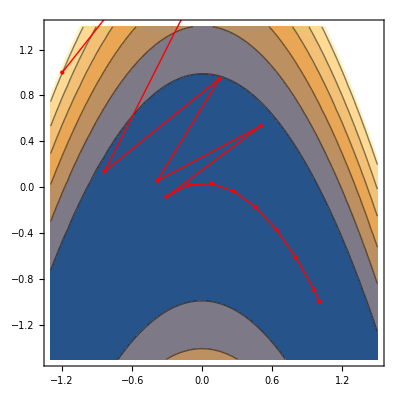

```mathematica
ContourPlot[(1-x)^2+100(-x^2-y)^2+1,{x,-1.3,1.5},{y,-1.5,1.4},Epilog->{Red,Line[pts],Point[pts]}]
```

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2},PlotTheme->"Detailed"]
```

-Graphics3D-